```mathematica
Xlk=XB1 = {6.5*10^-7,4.33*10^-6}
Xbk={6*10^-7,1.96*10^-6}
Xm=XA1={9.2*10^-7,5.01*10^-6}
XA2=XA6={6*10^-7,1.36*10^-6}
XA3=XA4={6*10^-7,4.12*10^-6}
```

{6.5×10^-7,4.33×10^-6}

{3/5000000,1.96×10^-6}

{9.2×10^-7,5.01×10^-6}

{3/5000000,1.36×10^-6}

{3/5000000,4.12×10^-6}

```mathematica
α=#⟦1⟧/#⟦2⟧&;
```

```mathematica
α[Xlk]
```

0.150115

```mathematica
αlk=Xlk⟦1⟧/Xlk⟦2⟧
αbk=Xbk⟦1⟧/Xbk⟦2⟧
αm=Xm⟦1⟧/Xm⟦2⟧
αB2=(αbk*αm)/αlk
```

0.150115

0.306122

0.183633

0.374472

```mathematica
wlk[l_]:=αlk*l;
wbk[l_]:=αbk*l;
wm[l_]:=αm*l;
wB2[l_]:=αB2*l;
```

{6.92774×10^-7,1.85×10^-6}

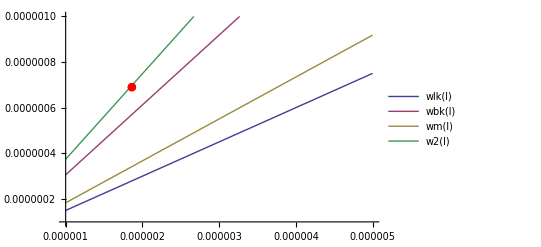

```mathematica
lB2=1.85*10^-6;
XB2 = {w2[l2], l2}
Show[Plot[{wlk[l],wbk[l],wm[l],w2[l]},{l,1*10^-6,5*10^-6},PlotRange->{1*10^-7,1*10^-6}, PlotLegends->"Expressions"],
ListPlot[{{l2,XB2⟦1⟧}},PlotStyle->Red,PlotMarkers->{"●",Medium}]]
```

```mathematica
Ilk=3.5*10^-9;
Iin=10*10^-9;
Ibk=3.5*10^-9
Im=αm*(αbk/Ibk)*((Ilk*Iin)/(αlk*α2))
```

3.5×10^-9

Set::wrsym: Symbol TraditionalForm`Im is Protected.

1.×10^-8

```mathematica
1.0314*10^-9
```